```mathematica
points = 4;
```

```mathematica
x = Extract[RandomReal[{0,3},{1,points}],{1}]
```

{1.61511,1.26359,0.877566,2.05786}

```mathematica
c = Extract[RandomReal[{2,3},{1,points}],{1}]
```

{2.56265,2.37062,2.09679,2.75115}

```mathematica
k = Extract[RandomReal[{1,1.2},{1,points}],{1}]
```

{1.09147,1.03723,1.12493,1.09767}

```mathematica
f = Function[{x1,x2,x3},x1*Exp[x2*x3]]
```

Function[{x1,x2,x3},x1 Exp[x2 x3]]

```mathematica
yData = Apply[f,{c,k,x}]
```

{14.9378,8.79146,5.62717,26.3346}

```mathematica
PlotData = Transpose@{x,yData};
```

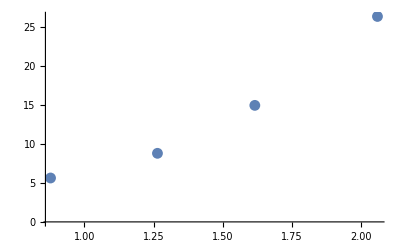

```mathematica
ListPlot[PlotData]
```

```mathematica
f1 = Function[{ci,ki,xi,yi},(ci*Exp[ki*xi]-yi)*Exp[ki*xi]];
```

```mathematica
f2 = Function[{ci,ki,xi,yi},(ci*Exp[ki*xi]-yi)*xi*ci*Exp[ki*xi]];
```

```mathematica
F = Function[{a,b},Total[f1[a,b,x,yData]]+Total[f2[a,b,x,yData]]];
```

```mathematica
Minimize[{Total[f1[a,b,x,yData]]+Total[f2[a,b,x,yData]],2<a<3,1<b<4},{a,b}]
```

{-558.246,{a→2.,b→1.}}

```mathematica
b
```

b

```mathematica
b
```

b

```mathematica
a2 = Extract[RandomReal[{-5,5},{1,2}],{1}];
```

```mathematica
b2 = Extract[RandomReal[{-5,5},{1,2}],{1}];
```

```mathematica
Apply[F,{a2,b2}]
```

Thread::tdlen: Objects of unequal length in {-0.727301, 1.1782}\ {1.61511, 1.26359, 0.877566, 2.05786} cannot be combined.

Thread::tdlen: Objects of unequal length in {-3.60029\ ⅇ^{-0.727301, 1.1782}\ {1.61511, 1.26359, 0.877566, 2.05786}, -2.36886\ ⅇ^{-0.727301, 1.1782}\ {1.61511, 1.26359, 0.877566, 2.05786}} + {-16.3387, -8.91235, -5.22429, -22.8037} cannot be combined.

General::stop: Further output of Thread :: tdlen will be suppressed during this calculation.

Total::tllen: Lists of unequal length in ⅇ^{-0.727301, 1.1782}\ {1.61511, 1.26359, 0.877566, 2.05786}\ ({-3.60029\ ⅇ^{-0.727301, 1.1782}\ {1.61511, 1.26359, 0.877566, 2.05786}, -2.36886\ ⅇ^{-0.727301, 1.1782}\ {1.61511, 1.26359, 0.877566, 2.05786}} + {-16.3387, -8.91235, -5.22429, -22.8037}) cannot be added.

Total::tllen: Lists of unequal length in ⅇ^{-0.727301, 1.1782}\ {1.61511, 1.26359, 0.877566, 2.05786}\ {-3.60029, -2.36886}\ ({-3.60029\ ⅇ^{-0.727301, 1.1782}\ {1.61511, 1.26359, 0.877566, 2.05786}, -2.36886\ ⅇ^{-0.727301, 1.1782}\ {1.61511, « 2 », « 18 »}} + {-16.3387, -8.91235, -5.22429, -22.8037})\ {1.61511, 1.26359, 0.877566, 2.05786} cannot be added.

Total[ⅇ^({-0.727301,1.1782} {1.61511,1.26359,0.877566,2.05786}) ({-3.60029 ⅇ^({-0.727301,1.1782} {1.61511,1.26359,0.877566,2.05786}),-2.36886 ⅇ^({-0.727301,1.1782} {1.61511,1.26359,0.877566,2.05786})}+{-16.3387,-8.91235,-5.22429,-22.8037})]+Total[ⅇ^({-0.727301,1.1782} {1.61511,1.26359,0.877566,2.05786}) {-3.60029,-2.36886} ({-3.60029 ⅇ^({-0.727301,1.1782} {1.61511,1.26359,0.877566,2.05786}),-2.36886 ⅇ^({-0.727301,1.1782} {1.61511,1.26359,0.877566,2.05786})}+{-16.3387,-8.91235,-5.22429,-22.8037}) {1.61511,1.26359,0.877566,2.05786}]